## Styling

```mathematica
dir=NotebookDirectory[]
```

/home/nicolas/git/talks/Séminaire CALIN/img/

```mathematica
(* Thickness *)
th=0.003;
```

```mathematica
(*Styling of the text*)
st=Directive[FontSize->15,FontFamily->"CMU Serif"];
stylize[text_]:=Style[text,st];
```

```mathematica
BostonBlue=RGBColor["#00688B"];
comp=RGBColor["#8B2300"];
```

```mathematica
SetOptions[{ListPlot,Plot},Frame->True,FrameStyle->st,PlotRange->All,PlotStyle->Black];
```

## Utility functions

```mathematica
(* string substitution *)
Sub[rule_,init_String,l_Integer]:=Nest[StringReplace[#,rule]&,init,l]
```

```mathematica
(* Height (integrated arrow field), can also be seen as the mode k=0 of the Fourier transform of the sequence of arrows *)
Heights[arrows_]:=Table[Total[arrows[[;;N]]],{N,1,Length[arrows]}];
```

```mathematica
(* maximum of the height distribution *)
MaxHeights[heights_]:=Block[{absheights=Abs[heights]},Table[Max[absheights[[;;N]]],{N,1,Length[heights]}]];
```

```mathematica
(* for a string of an even number of A and B, replace every couple by the corresponding arrow *)
ToArrowAlphabet[string_]:=StringReplace[string,{"AB"->"R","BA"->"L","AA"->"Ia","BB"->"Ib"}];
(* return the vector counting the number of arrows *)
ArrowCountVec[string_]:=StringCount[string,#]&/@{"R","L","Ia","Ib"};
```

```mathematica
(* periodic approximant of a sequence seq of two letters, in normal numbering *)
h[ρ_,seq_]:=Block[{jump,tbl,ar,n=StringLength[seq]},
jump[j_]:=If[StringTake[seq,{j}]=="B",1.,ρ];

(* nearest neighbour hopppings *)
tbl=Table[{i,i+1}->jump[i],{i,1,n-1}];
(* boundary conditions for the nearest neighbour hoppings *)
PrependTo[tbl,{1,n}->jump[n]];

(* transform to an array and construct the lower diagonal part *)
ar=SparseArray[tbl,{n,n}];
Normal[ar+ConjugateTranspose[ar]]
]
```

For the E=0 level to exist, we need an odd number of letters. But we also need the system to be bipartite for the wavefunction to be nonzero only on one site over two → open boundary conditions.

```mathematica
(* open approximant of a sequence seq of two letters, in normal numbering *)
ho[ρ_,seq_]:=Block[{jump,tbl,ar,n=StringLength[seq]},
jump[j_]:=If[StringTake[seq,{j}]=="B",1.,ρ];

(* nearest neighbour hopppings *)
tbl=Table[{i,i+1}->jump[i],{i,1,n-1}];

(* transform to an array and construct the lower diagonal part *)
ar=SparseArray[tbl,{n,n}];
Normal[ar+ConjugateTranspose[ar]]
]
```

```mathematica
(* zip lists *)
Zip[l1_List,l2_List]:=MapThread[{#1,#2}&,{l1,l2}];
```

## Idos periodic chain

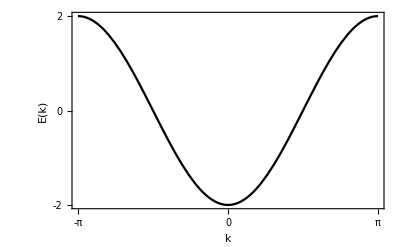

/home/nicolas/git/talks/Séminaire CALIN/img/spectre_chaine_periodique.pdf

```mathematica
Plot[-2Cos[k],{k,-π,π},FrameTicks->{{{-2,0,2},None},{{-Pi,0,Pi},None}},FrameLabel->stylize/@{"k","E(k)"}]
Export[NotebookDirectory[]<>"spectre_chaine_periodique.pdf",%]
```

```mathematica
(* idos of the periodic chain *)
idosp[ϵ_]:=If[ϵ≤-2,0,If[ϵ≥2,1,1/2+1/π ArcSin[ϵ/2]]]
```

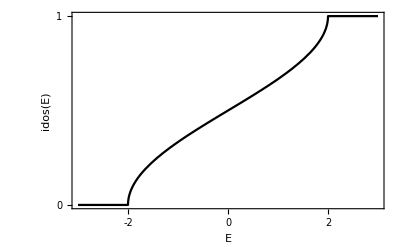

/home/nicolas/git/talks/Séminaire CALIN/img/idos_chaine_periodique.pdf

```mathematica
Plot[idosp[E],{E,-3,3},FrameTicks->{{{0,1},None},{{-2,0,2},None}},FrameLabel->stylize/@{"E","idos(E)"}]
Export[NotebookDirectory[]<>"idos_chaine_periodique.pdf",%]
```

## Fibonacci substitution

```mathematica
(* Fibonacci substitution *)
FiboSub[l_,C0_String]:=Sub[{"A"->"AB","B"->"A"},C0,l];
(* Fibonacci substitution, composed 3 times *)
FiboSub3[l_,C0_String]:=Sub[{"A"->"ABAAB","B"->"ABA"},C0,l];
ArrowSub[l_,C0_String]:=Sub[{"R"->"RILL","L"->"RILR","I"->"RILLR"},C0,l];
FiboArrows2[string_]:=StringPartition[string,1]/.{"R"->1,"L"->-1,"I"->0};
LocalEnvs={"RR","RI","LL","IL","LR"};
HeightCount[ArrowString_]:=StringCount[ArrowString,#]&/@LocalEnvs;
LocalEnvs2={"R","L","I"};
HeightCount2[ArrowString_]:=StringCount[ArrowString,#]&/@LocalEnvs2;
(* the field of arrows *)
FiboArrows[l_]:=StringPartition[FiboSub3[l,"AB"],2]/.{"AB"->1,"BA"->-1,"AA"->0};
```

### Height field and central state

FiboArrows[l] gives the heights on the chain of length Fibonacci[3l+3].

```mathematica
arrows=FiboArrows[7];
FiboHeights=Heights[arrows];
```

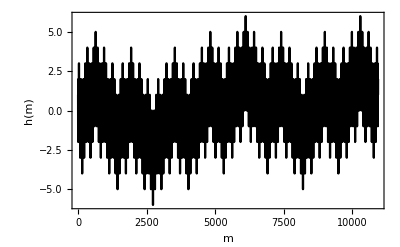

/home/nicolas/git/talks/Séminaire CALIN/img/height_fibo.pdf

```mathematica
(* the height max grows logarithmically, and the height function goes to 0 arbitrarily far from the origin *)
ListPlot[FiboHeights[[;;Fibonacci[3*7]]],Joined->True,FrameLabel->stylize/@{"m","h(m)"}]
Export[dir<>"height_fibo.pdf",%]
```

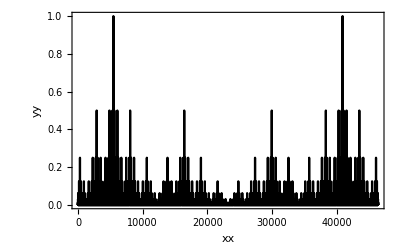

/home/nicolas/git/talks/Séminaire CALIN/img/central_state_fibo.pdf

```mathematica
(* the corresponding central state *)
ρ=0.5;
(* the intensity is 0 every two sites *)
centralState=Riffle[ConstantArray[0,Length[arrows]],ρ^(FiboHeights)];
(* normalize *)
centralState/=Max[centralState];
ListPlot[centralState,Joined->True,FrameLabel->stylize/@{"xx","yy"}]
Export[dir<>"central_state_fibo.pdf",%]
```

### IDOS

```mathematica
mat=ho[0.8,FiboSub3[5,"B"]];
{vals,vecs}=Eigensystem[mat];
o=Ordering[vals];
vals=vals[[o]];
vecs=vecs[[o]];
```

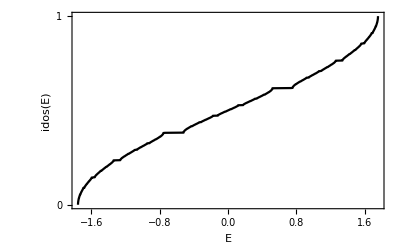

/home/nicolas/git/talks/Séminaire CALIN/img/idos_fibo.pdf

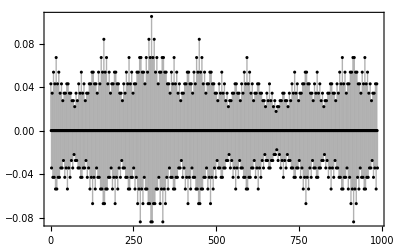

```mathematica
L=Length[vals];
ListPlot[Zip[vals,Range[L]/L],FrameLabel->stylize/@{"E","idos(E)"},Joined->True,FrameTicks->{{{0,1},None},{Automatic,None}}]
Export[dir<>"idos_fibo.pdf",%]
idxCenter=(Length[vals]+1)/2;
ListPlot[vecs[[idxCenter]],Filling->Axis,PlotRange->All]
```

```mathematica
ListPlot[Zip[vals,Range[L]/L],FrameLabel->stylize/@{"E","idos(E)"},Joined->True,FrameTicks->{{{0,1},None},{Automatic,None}}]
```

-Graphics-